Last modified on: Tuesday, July 10, 2018 at 22:49

Author Info

Andrew Wheeler

Carlo Barbieri

Hamilton College

Poster Session Content

Visualizing Your Inbox

The tools in the Wolfram Language’s Email connection paclet can be very easily used to present and visualize meaningful information about your inbox, including who emails you, who you have conversations with, most common meaningful words, and more. The package itself is experimental and very interesting in how it treats each item in any given mailbox, so discovering how each element could be searched and how its details could be presented ended up not being a trivial task.

Add the most representative image of your project here. (We recommend just 1 image, if you add more, we will make a collage of the images.)

-Graphics--Graphics-

Many analytical methods transitioned very well to the MailItem entity, and in doing so clearly explained some very interesting conclusions about how I use my inbox. You typically don’t realize quite how many spam or advertisement emails you get on a daily basis, not to mention various alerts from social media platforms . In the end, a lot of analytical ideas I would have liked to explore proved tough to access, as some important pieces of information were missing or algorithmically very difficult to sort and store, and even more so to generalize  to any given user’s mail account.

Further exploration within the MailItem and MailServerConnection functions would definitely include generalizing functionality to all folders of a user’s mail account, and generalizing to work on any given mail servers, as each different provider (gmail, yahoo, etc) uses slightly different tags for a message. More specifically, it would be very interesting to find and group all emails from specific group of recipients. Analysis on larger conversation groups could show very interesting results, including: who gets left out of conversations most often, how quickly do certain groups reply, which groups tend to add more recipients as the email chain continues via cc’s and forwarding.

Note: Everything above this bar is your poster.Make sure it fits on a single page. "Preview Poster"

End of School Presentation Content

In addition to the poster content, include other content to present at the 2 minute presentation for end of school. Use the buttons below to add more sections."Add Header""Add Text""Add Code or Image"

Quick note!

A lot of the cool bits and functionality are up on Github because it would take longer than two minutes to go through, so here’s just two functions. The setup is at the top, which includes the login to the email server and setting up variables so the functions below do not have to reach to the server every time they need to grab information about an email.

Visualization Functions

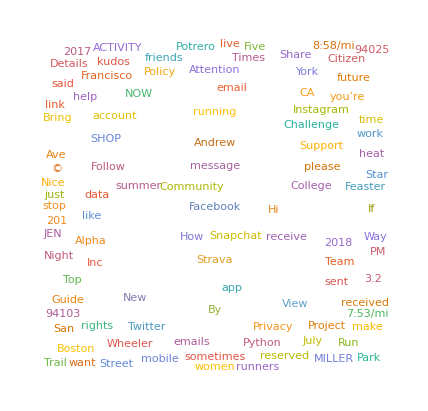
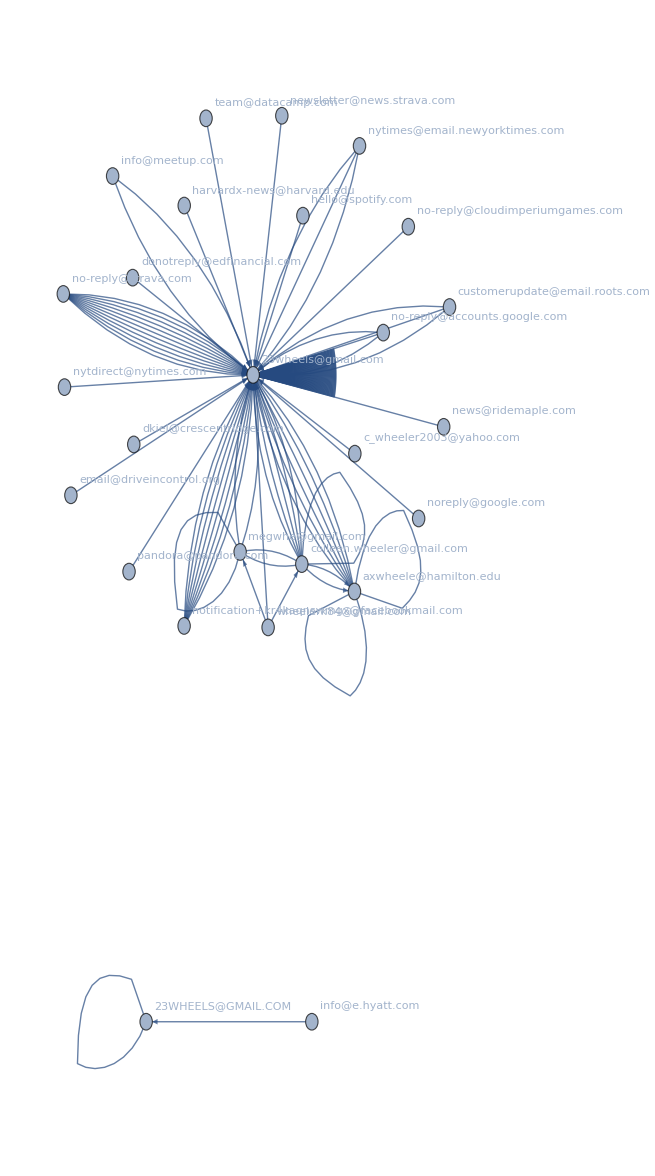
connectInbox[server_String,username_String]:=(
mail=MailServerConnect["imap."<>server,username];
inbox=mail["INBOX"];
sent=mail["[Gmail]/Sent Mail"];)
connectInbox["gmail.com","23wheels"]
emailsFromInbox=inbox[-50;;-1];

emailWordCloud[number_Integer?Positive]:=(
noList=WordList["Stopwords"];
WordCloud[
WordCounts[
StringJoin[
Table[
inbox[-x]["Body"],
{x,number}
]]],
WordSelectionFunction→
((StringLength[#]<10)&&
!(MemberQ[noList,#])&&
(!NumberQ[#])&)
])
emailWordCloud[25]
-Graphics-

commonEmailers=TakeLargest[Counts@Map[#["FromAddress"]&,emailsFromInbox],10];
PieChart[Values[commonEmailers],ChartLabels→Placed[Keys[commonEmailers],"RadialOuter"]]
-Graphics-

edges=Flatten@Map[
Function[{message},
fromList=If[StringQ@message["FromAddress"],message["FromAddress"],"weird"];
toList=Select[message["ToAddressList"],StringQ];
ccList=Select[message["ToAddressList"],StringQ];
If[
fromList==="weird",Nothing,
{
DirectedEdge[fromList,#]&/@ccList,
Flatten@Outer[UndirectedEdge,toList,ccList]
}]],
emailsFromInbox
];
Graph[edges,VertexLabels→"Name"]
-Graphics-

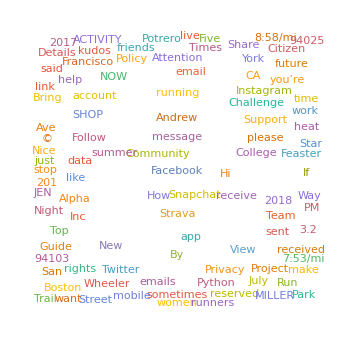

-Graphics-

Note: Everything above this bar is in your 2 minute presentation. Make sure it fits on 2 slides. "Preview Presentation"

Detailed Project Notes

#### Main Results in Detail

#### Code

Provide one of:

Link to the GitHub

Explicit code

#### Written Content / Lesson Plans

#### Conclusions in Detail

#### All Visualizations

#### Data Sources Links/References

#### Future Directions

#### Background Info Links/References

#### Keywords

Provide keywords as items

< keyword 1 >

< keyword 2 >

#### Other information